# Testing singleSlipSolution.xml

In this notebook, we examine slip along a plane that is rotated to the global axes.

<!-- =========================================================================================== -->

     <ParameterList name=”Materials”>

          <ParameterList name=”metal_fcc”>


<!-- ~~~~~~~~~ Specify material model ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->

               <ParameterList name=”Material Model”>

                    <Parameter name=”Model Name”
                               type=”string”
                               value=”CrystalPlasticity”/>

               </ParameterList>


<!-- ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->
<!-- ~~~~~~~~~ Set program controls ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->
<!-- ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->

               <Parameter name=”Integration Scheme”
                          type=”string”
                          value=”Implicit”/>

               <Parameter name=”Implicit Integration Relative Tolerance”
                          type=”double”
                          value=”1.0e-35”/>

               <Parameter name=”Implicit Integration Absolute Tolerance”
                          type=”double”
                          value=”1.0e-10”/>

               <Parameter name=”Implicit Integration Max Iterations”
                          type=”int”
                          value=”100”/>

       <ParameterList name=”Crystal Elasticity”>

                    <Parameter name=”C11”
                               type=”double”
                               value=”204.6e3”/>

                    <Parameter name=”C12”
                               type=”double”
                               value=”137.7e3”/>

                    <Parameter name=”C44”
                               type=”double”
                               value=”126.2e3”/>

                    <Parameter name=”Basis Vector 1”
                               type=”Array(double)”
                               value=”{-0.09175170953613698, | 0.908248290463863, | 0.408248290463863}”/>

                    <Parameter name=”Basis Vector 2”
                               type=”Array(double)”
                               value=”{0.908248290463863, | -0.09175170953613698, | 0.408248290463863}”/>

                    <Parameter name=”Basis Vector 3”
                               type=”Array(double)”
                               value=”{0.408248290463863, | 0.408248290463863, | -0.816496580927726}”/>

               </ParameterList>
               
        <!-- ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->
<!-- ~~~~~~~~~ Set crystal plasticity parameters ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->
<!-- ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->

               <Parameter name=”Number of Slip Systems”
                          type=”int”
                         value=”1”/>

<!-- ~~~~~~~~~ Specify slip system 1 ~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~~ -->

               <ParameterList name=”Slip System 1”>

                    <Parameter name=”Slip Direction”
                               type=”Array(double)”
                               value=”{-1.0, 1.0, 0.0}”/>

                    <Parameter name=”Slip Normal”
                               type=”Array(double)”
                               value=”{1.0, 1.0, 1.0}”/>

                    <Parameter name=”Tau Critical”
                               type=”double”
                               value=”122.0”/>

                    <Parameter name=”Gamma Dot”
                               type=”double”
                               value=”1.0”/>

                    <Parameter name=”Gamma Exponent”
                               type=”double”
                               value=”50.0”/>

                    <Parameter name=”Hardening”
                               type=”double”
                               value=”0.0”/>

                    <Parameter name=”Hardening Exponent”
                               type=”double”
                               value=”0.0”/>

               </ParameterList>

## State basis for material coordinate system

Looking at a basis derived to simplify Schmid tensor and E3 (for debugging)

```mathematica
basis = {{1/Sqrt[6]-1/2,1/Sqrt[6]+1/2,1/Sqrt[6]},{1/Sqrt[6]+1/2,1/Sqrt[6]-1/2,1/Sqrt[6]},{1/Sqrt[6],1/Sqrt[6],-2/Sqrt[6]}};
MatrixForm[basis];
MatrixForm[N[basis,16]]
checkBasis = Norm[Simplify[basis . Transpose[basis]-IdentityMatrix[3]]];
checkDot12 = Simplify[basis[[1,All]] . basis[[2,All]]];
checkDot13 = Simplify[basis[[1,All]] . basis[[3,All]]];
checkDot23 = Simplify[basis[[2,All]] . basis[[3,All]]];
checkCross12= Norm[Simplify[Cross[basis[[1,All]],basis[[2,All]]]-basis[[3,All]]]];
checkCross23 = Norm[Simplify[Cross[basis[[2,All]],basis[[3,All]]]-basis[[1,All]]]];
checkCross31 = Norm[Simplify[Cross[basis[[3,All]],basis[[1,All]]]-basis[[2,All]]]];
checkDet=Det[basis]-1;
```

(-0.09175170953613698 | 0.908248290463863 | 0.408248290463863
0.908248290463863 | -0.09175170953613698 | 0.408248290463863
0.408248290463863 | 0.408248290463863 | -0.816496580927726)

## Derive direction cosine matrix for coordinate transformations

```mathematica
orientation = Transpose[basis];
MatrixForm[orientation]
```

(-1/2+1/(√6) | 1/2+1/(√6) | 1/(√6)
1/2+1/(√6) | -1/2+1/(√6) | 1/(√6)
1/(√6) | 1/(√6) | -√(2/3))

## Transform slip and normal directions to global coordinate system

```mathematica
slipdirectionGlobal = Simplify[orientation . {{-1/Sqrt[2]},{1/Sqrt[2]},{0}}];
slipnormalGlobal = Simplify[orientation . {{1/Sqrt[3]},{1/Sqrt[3]},{1/Sqrt[3]}}];
MatrixForm[slipdirectionGlobal];
MatrixForm[slipnormalGlobal];
```

## Create Schmid tensor

```mathematica
projection =Outer[Times,Transpose[slipdirectionGlobal][[1]],Transpose[slipnormalGlobal][[1]]];
MatrixForm[projection]
```

(1/2 | 1/2 | 0
-1/2 | -1/2 | 0
0 | 0 | 0)

## Define velocity gradient Lp_{n+1}

```mathematica
Lpnplus1 = gammaDot*projection;
MatrixForm[Lpnplus1];
```

## Find Fp_{n+1} through the exponential map

This is the form of Fp.

```mathematica
Fpnplus1 = MatrixExp[Δt*Lpnplus1] . {{Fpn11,Fpn12,Fpn13},{Fpn21,Fpn22,Fpn23},{Fpn31,Fpn32,Fpn33}} /. {Δt*gammaDot -> Δγ};
MatrixForm[Fpnplus1];
```

## Impose uniaxial strain and find Fe_{nplus1} and Ee_{nplus1}

```mathematica
Fapplied = {{1+c*t,0,0},{0,1,0},{0,0,1}};
```

```mathematica
Fenplus1 = Simplify[Fapplied . Inverse[Fpnplus1]];
Cenplus1 = Transpose[Fenplus1] . Fenplus1;
Id3 = {{1,0,0},{0,1,0},{0,0,1}};
Eenplus1 = Simplify[1/2*(Cenplus1 - Id3)];
MatrixForm[Eenplus1];
```

## Calculate and rotate the elasticity tensor

```mathematica
elasTensor = Table[i*j*k*l*0,{i,1,3},{j,1,3},{k,1,3},{l,1,3}];
Do[elasTensor[[i,i,i,i]] = c11;
Do[elasTensor[[i,i,j,j]] = c12;
elasTensor[[j,j,i,i]] = c12;
elasTensor[[i,j,i,j]] = c44;
elasTensor[[j,i,j,i]] = c44;
elasTensor[[i,j,j,i]] = c44;
elasTensor[[j,i,i,j]] = c44,
{j,i+1,3}],{i,1,3}]
MatrixForm[elasTensor];
```

```mathematica
transformElasTensor = Table[i*j*k*l*0,{i,1,3},{j,1,3},{k,1,3},{l,1,3}];
Do[ Do[transformElasTensor[[w,v,u,t]]= transformElasTensor[[w,v,u,t]] + elasTensor[[p,q,r,s]]*orientation[[p,w]]*
orientation[[q,v]]*orientation[[r,u]]*orientation[[s,t]],{s,1,3},{r,1,3},{q,1,3},{p,1,3}],{t,1,3},{u,1,3},{v,1,3},{w,1,3}];
MatrixForm[transformElasTensor];
```

## Get 2nd PK stress in the intermediate configuration

```mathematica
Snplus1 = Table[i*j*0,{i,1,3},{j,1,3}];
Do[
Do[Snplus1[[i,j]] = Snplus1[[i,j]] + transformElasTensor[[i,j,k,l]]*Eenplus1[[k,l]],
{l,1,3},{k,1,3}],{j,1,3},{i,1,3}]
MatrixForm[Snplus1];
```

## Form residual as a function of material parameters and state

```mathematica
tau1 = Tr[Transpose[Cenplus1.Snplus1] . projection];
(*tau1 = Tr[Transpose[Snplus1] . projection];*)
partR = Δt*gammaDot0*(Abs[tau1]/tau0)^k*signtau1;
R = -Δγ + partR;
parameters = {c11 -> 204600., c12 -> 137700., c44 -> 126200.,c -> 1,tau0 -> 122., gammaDot0 -> 1, k -> 50};
state = {Fpn11 -> 1, Fpn12 -> 0, Fpn13 -> 0, Fpn21 -> 0, Fpn22 -> 1, Fpn23 -> 0, Fpn31 -> 0, Fpn32 -> 0, Fpn33 -> 1};
Rparam = R /. parameters;
tau1param =tau1 /. parameters;
Reval = Rparam /. {signtau1 -> Sign[tau1param]} /. state;
```

## Loop through time to construct a solution

```mathematica
iloop = 1;
tn = 0;
finalTime = 1/100;
numberSteps = 50;
timeIncrement = finalTime/numberSteps;
times = Table[i*0,{i,1,numberSteps+1}];
residuals = Table[i*0,{i,1,numberSteps+1}];
slips = Table[i*0,{i,1,numberSteps+1}];
taus = Table[i*0,{i,1,numberSteps + 1}];
tangents = Table[i*0,{i,1,numberSteps + 1}];
axialStress = Table[i*0,{i,1,numberSteps +1}];
cauchy=Table[i*j*k*0,{k,1, numberSteps + 1},{i,1,3},{j,1,3}];
FOut = Table[i*j*k*0,{k,1, numberSteps + 1},{i,1,3},{j,1,3}];
FpOut = Table[i*j*k*0,{k,1, numberSteps + 1},{i,1,3},{j,1,3}];
state = {Fpn11 -> 1, Fpn12 -> 0, Fpn13 -> 0, Fpn21 -> 0, Fpn22 -> 1, Fpn23 -> 0, Fpn31 -> 0, Fpn32 -> 0, Fpn33 -> 1}; 
 
(* Initialize output for t = 0. Everything besides tangent, F, and Fp is zero*)
temp = D[Rparam,Δγ ] /.  {signtau1 -> Sign[tau1param]}/. state /. {Δt -> 0, t -> 0}/. {Δγ  -> 0};
tangents[[iloop]] = FunctionExpand[temp, Assumptions -> {Element[Δγ, Reals]}];
FOut[[iloop,All,All]] = Fapplied /. parameters /. {t -> 0};
FpOut[[iloop,All,All]] = (Fpnplus1 /. state) /. Δγ -> 0;


(* Increment time *)
iloop = iloop + 1;
tnplus1 = timeIncrement;
```

```mathematica
(* Loop for solution *)
While[tnplus1 ≤ finalTime,
(* Increment time *)
times[[iloop]] = tnplus1;
(* Residual is all you need to find the slip increment. Keep signtau *)
Reval = Rparam /.  {signtau1 -> Sign[tau1param]}/. state;
RevalTime = Reval /. {Δt -> timeIncrement, t -> tnplus1};
slipIncrement=Δγ/.FindRoot[RevalTime ,{Δγ,slips[[iloop-1]]},MaxIterations->10000,AccuracyGoal->20,PrecisionGoal->20];
(*slipIncrement = Max[Δγ/.NSolve[RevalTime == 0, Δγ,Reals]];*)
slips[[iloop]]= slips[[iloop -1]] + slipIncrement;
residuals[[iloop]] = RevalTime /. {Δγ -> slipIncrement};

(* Get the tangent for post processing *)
temp = D[Rparam,Δγ ] /.  {signtau1 -> Sign[tau1param]}/. state /. {Δt -> timeIncrement, t -> tnplus1}/. {Δγ  -> slipIncrement};
tangents[[iloop]] = FunctionExpand[temp, Assumptions -> {Element[Δγ, Reals]}];

(* Get shear stress for post processing *)
tau1eval = tau1param  /. state;
tau1evalTime = tau1eval /. {Δt -> timeIncrement, t -> tnplus1};
taus[[iloop]] = tau1evalTime /. Δγ -> slipIncrement;

(* Get F for post processing *)
FOut[[iloop,All,All]] = Fapplied /. parameters /. {t -> tnplus1};
(* Get stresses for post processing *)
Fenplus1Eval = Fenplus1 /. parameters /. state  /. {Δt -> timeIncrement, t -> tnplus1, Δγ -> slipIncrement};
Snplus1Eval = Snplus1 /. parameters /. state /. {Δt -> timeIncrement, t -> tnplus1, Δγ -> slipIncrement};
cauchy[[iloop,All,All]]=1/Det[Fenplus1Eval]* Fenplus1Eval .  Snplus1Eval . Transpose[Fenplus1Eval];
axialStress[[iloop]] = cauchy[[iloop,1,1]];

(* Get ready for next step and save Fpnplus1 *)
Fpnplus1Eval = (Fpnplus1 /. state) /. Δγ -> slipIncrement;
FpOut[[iloop,All,All]] = Fpnplus1Eval;
state = {Fpn11 -> Fpnplus1Eval[[1,1]], Fpn12 ->  Fpnplus1Eval[[1,2]], Fpn13 ->  Fpnplus1Eval[[1,3]], Fpn21 ->  Fpnplus1Eval[[2,1]], Fpn22 ->  Fpnplus1Eval[[2,2]], Fpn23 ->  Fpnplus1Eval[[2,3]], Fpn31 ->  Fpnplus1Eval[[3,1]], Fpn32 ->  Fpnplus1Eval[[3,2]], Fpn33 ->  Fpnplus1Eval[[3,3]]}; 
iloop = iloop + 1;
tnplus1 = tnplus1 + timeIncrement]
```

## Plotting results for sanity check

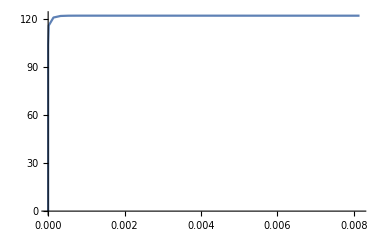

```mathematica
ListLinePlot[Transpose[{slips,taus}]]
```

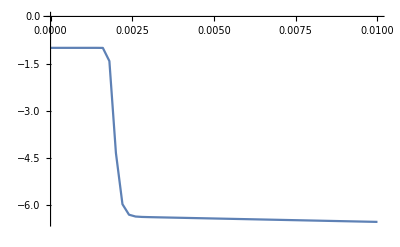

```mathematica
(*ListLinePlot[Transpose[{times,slips}]]*)
ListLinePlot[Transpose[{times,tangents}]]
```

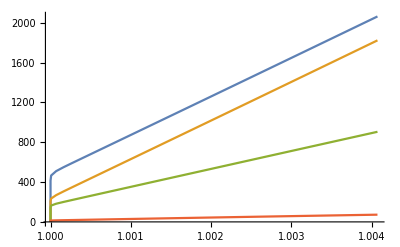

```mathematica
ListLinePlot[{Transpose[{FpOut[[All,1,1]],cauchy[[All,1,1]]}],
Transpose[{FpOut[[All,1,1]],cauchy[[All,2,2]]}],
Transpose[{FpOut[[All,1,1]], cauchy[[All,3,3]]}],
Transpose[{FpOut[[All,1,1]], cauchy[[All,1,2]]}]}]
```

## Writing results to file for comparison

```mathematica
nbHome = NotebookDirectory[];
filenameSlipsTausMath = StringJoin[nbHome,"slipsTausMath.dat"];
optstr = OpenWrite[filenameSlipsTausMath];
Do[tempstr = StringJoin[ToString[CForm[N[slips[[i]]]]],",",ToString[CForm[N[taus[[i]]]]],"\n"];
WriteString[optstr,tempstr];,
{i,1,numberSteps+1}]
Close[optstr ];
filenamefpCauchyMath = StringJoin[nbHome,"fpCauchy11Math.dat"];
optstr = OpenWrite[filenamefpCauchyMath];
Do[tempstr = StringJoin[ToString[CForm[N[FpOut[[i,1,1]]]]],",",ToString[CForm[N[cauchy[[i,1,1]]]]],"\n"];
WriteString[optstr,tempstr];,
{i,1,numberSteps+1}]
Close[optstr ];
```

## Printing results for verification

```mathematica
MatrixForm[Transpose[{slips,taus}]];
MatrixForm[Transpose[{FpOut[[All,1,1]],cauchy[[All,1,1]]}]];
MatrixForm[Transpose[{FOut[[All,1,1]],cauchy[[All,1,1]]}]];
N[residuals,16];
NumberForm[slips,16];
NumberForm[taus,16];
NumberForm[FpOut[[All,1,1]],16];
NumberForm[FOut[[All,1,1]],16];
```

## Reading results from file for comparison

LCM has an extra step that happens just prior to the last step. Roundoff the the boundary condition is causing issues. We elimnate the second to last step, number of steps + 1.

```mathematica
filenameSlipsTaus = StringJoin[nbHome,"slipsTaus.dat"];
filenamefpCauchy = StringJoin[nbHome,"fpCauchy11.dat"];
sT =Import[filenameSlipsTaus,"Table"];
fC = Import[filenamefpCauchy,"Table"];
fC[[numberSteps+1,All]] = fC[[numberSteps+2,All]];
fC = Drop[fC,-1];
sT[[numberSteps+1,All]] = sT[[numberSteps+2,All]];
sT = Drop[sT,-1];
```

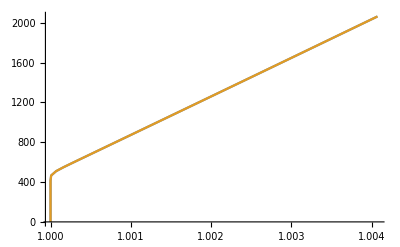

```mathematica
ListLinePlot[{Transpose[{FpOut[[All,1,1]],cauchy[[All,1,1]]}],fC}]
```

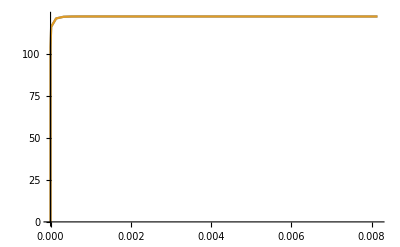

```mathematica
ListLinePlot[{Transpose[{slips,taus}],sT}]
```

Comment: What is the residual on the 8th step that causes the largest difference in the Cauchy stress? In LCM, the residual was on the order of 1e-11 which is probably the difference in the solutions. Further tightened the absolute tolerance in the slip residual (1e-14) to increase agreement with Mathematica.

```mathematica
relErrorFp = Table[0*i,{i,1,numberSteps}];
relErrorCauchy = Table[0*i,{i,1,numberSteps}];
absErrorSlip = Table[0*i,{i,1,numberSteps}];
relErrorTau =  Table[0*i,{i,1,numberSteps}];
Do[relErrorFp[[i]] =   Abs[(FpOut[[i+1,1,1]] -fC[[i+1,1]])/FpOut[[i+1,1,1]]];
relErrorCauchy[[i]] =   Abs[(cauchy[[i+1,1,1]] -fC[[i+1,2]])/cauchy[[i+1,1,1]]];
absErrorSlip[[i]] =   Abs[slips[[i+1]] -sT[[i+1,1]]];
relErrorTau[[i]] = Abs[(taus[[i+1]] - sT[[i+1,2]])/taus[[i+1]]];
,{i,numberSteps}]
```

```mathematica
Max[relErrorFp]
Max[relErrorCauchy]
Max[absErrorSlip]
Max[relErrorTau]
```

5.74974×10^-15

5.36009×10^-13

8.30239×10^-15

4.86719×10^-12